### Explicit Examples

```mathematica
α = ({{α1}, {α2}, {α3}, {α4}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
β3=({{β31}, {β32}, {β33}, {β34}});
β4=({{β41}, {β42}, {β43}, {β44}});
A0=({{0, 0, 0, 0}, {A021, 0, 0, 0}, {A031, A032, 0, 0}, {A041, A042, A043, 0}}); (* A0=({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}}); *)
A1=({{0, 0, 0, 0}, {A121, 0, 0, 0}, {A131, A132, 0, 0}, {A141, A142, A143, 0}}); (* Subscript[A, 1]=({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A113, A134}, {A141, A142, A143, A144}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}}); *)
B1=({{0, 0, 0, 0}, {B121, 0, 0, 0}, {B131, B132, 0, 0}, {B141, B142, B143, 0}}); (* Subscript[B, 1]=({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}}); *)
e = ({{1}, {1}, {1}, {1}});
constraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_]:={α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0}
higherConstraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_] := {α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0,A021 α2+A031 α3+A032 α3+A041 α4+A042 α4+A043 α4==1/2,B021 α2+B031 α3+B032 α3+B041 α4+B042 α4+B043 α4==1,B021^2 α2+(B031+B032)^2 α3+(B041+B042+B043)^2 α4==3/2,A121 β12+A131 β13+A132 β13+A141 β14+A142 β14+A143 β14==1,A121 β22+A131 β23+A132 β23+A141 β24+A142 β24+A143 β24==0,A121 β32+A131 β33+A132 β33+A141 β34+A142 β34+A143 β34==-1,A121 β42+A131 β43+A132 β43+A141 β44+A142 β44+A143 β44==0,B121^2 β12+(B131+B132)^2 β13+(B141+B142+B143)^2 β14==1,B121^2 β22+(B131+B132)^2 β23+(B141+B142+B143)^2 β24==0,B121^2 β32+(B131+B132)^2 β33+(B141+B142+B143)^2 β34==-1,B121^2 β42+(B131+B132)^2 β43+(B141+B142+B143)^2 β44==2,B121 B132 β13+(B121 B142+(B131+B132) B143) β14==0,B121 B132 β23+(B121 B142+(B131+B132) B143) β24==0,B121 B132 β33+(B121 B142+(B131+B132) B143) β34==0,B121 B132 β43+(B121 B142+(B131+B132) B143) β44==1,1/2 (A132 B021 β13+(A142 B021+A143 (B031+B032)) β14)+1/3 (A132 B021 β33+(A142 B021+A143 (B031+B032)) β34)==0}
Get["stableRegionsEq.mx"]
zmin = -14;
zmax = 1;
wmin = -3;
wmax = 3;
ymin = -4;
ymax = 4;
```

jOpt.9091807.comet-31-04

{0.235976,-0.0957746,1.09577,-0.615341,-1.42452,3.03986,0.930643,1.00923,-0.00922663,0.921083,0.143562,-0.0646444,0.620572,1.8806,-0.266295,3.09501,4.30018,-2.33226,-0.964698,0.0731439,-2.47721,-1.02785,-0.0484431,-2.63084,0.0446284,0.596017,0.34485,0.0145043,-0.206498,2.97731,-2.83363,1.06282,-0.127311,1.83561,-2.73359,1.0253,1.2065,-2.97732,2.83364,-1.06282,-0.0416661,0.60074,-1.14577,0.586699}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

16.704

-Graphics3D-

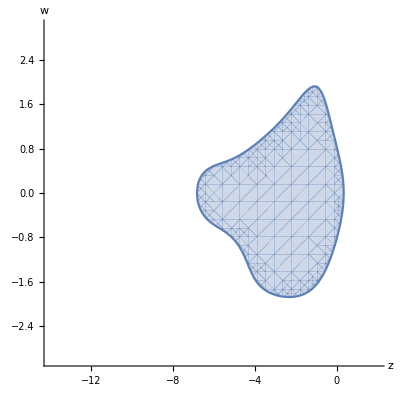

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.2359760533743713,-0.09577455750751056,1.0957744377029883,-0.6153407580085136,-1.4245163708917585,3.039857065434202,0.9306426751148328,1.0092266342048692,-0.009226634204869081,0.9210826830841823,0.14356167099739364,-0.06464435408158922,0.6205718656852524,1.8806036844442322,-0.2662953129236468,3.095008424598287,4.300176313345955,-2.3322553814437,-0.9646983671229188,0.07314388300786438,-2.4772051781460727,-1.027853248838071,-0.048443072407040697,-2.630841778235683,0.04462844902337111,0.5960170570564689,0.3448501467035236,0.01450427118501567,-0.20649757675825592,2.977309369696076,-2.833630774962583,1.0628190666434316,-0.12731139384162451,1.8356075600871133,-2.7335940859575807,1.025298037619955,1.2065000679837121,-2.9773178687780777,2.8336403534317456,-1.0628225671595946,-0.04166606288874141,0.6007396654286985,-1.1457727013981074,0.5866991302217075}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091813.comet-30-09

{0.102474,1.01134,-0.0113363,0.38917,0.616303,-0.00547314,0.598819,0.941917,0.0580823,1.10281,-0.239285,0.136474,0.339676,0.329443,-0.110499,1.04969,0.000261334,0.133256,0.773834,0.417534,-0.61972,1.2428,1.41639,-0.78574,1.11038,-0.680068,-0.577589,1.14728,0.27051,-0.674286,1.01565,0.388125,-0.727762,1.81405,-0.785945,-0.300344,0.72949,0.674285,-1.01565,-0.388125,0.870909,-2.17087,0.363994,0.935962}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

13.2435

-Graphics3D-

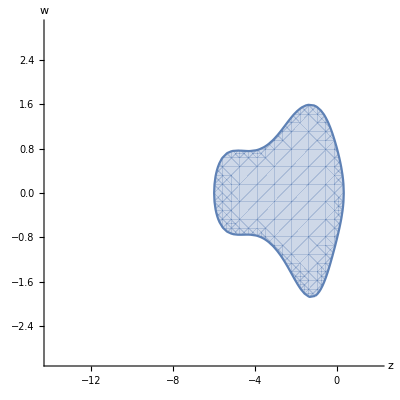

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.1024743167863612,1.01133627557693,-0.011336278630660487,0.38916979549451575,0.6163033435596011,-0.005473139084546834,0.5988190465819249,0.9419171671140063,0.05808227764738066,1.1028107794600093,-0.23928544474925728,0.13647434558232233,0.33967608278217304,0.3294429097814644,-0.11049854034638505,1.0496856841184943,0.0002613340480150756,0.13325585254125796,0.7738341802388574,0.4175338099440435,-0.619719704481535,1.242803266369781,1.4163930551020356,-0.7857401755804172,1.1103783362402675,-0.6800677971697444,-0.577588590737696,1.1472780375950937,0.2705100874582641,-0.67428575533376,1.0156504879792536,0.38812521066071975,-0.727762438311749,1.8140516806205318,-0.7859447692998686,-0.30034447587223423,0.7294902400158448,0.6742853999022742,-1.0156505482164462,-0.3881250911925831,0.8709094799650314,-2.1708658565869943,0.3639938755692357,0.9359624907797618}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091817.comet-31-03

{0.515668,2.56928,-1.56928,0.282936,0.826725,-0.109661,0.756466,0.861818,0.138182,0.940483,0.244237,-0.18472,1.32567,1.89178,-0.671652,-0.406994,-0.204881,0.00567568,-0.869751,-0.300029,-1.68083,2.60572,-1.08044,0.0779824,0.0551888,0.918401,-0.110322,0.136732,-0.268387,1.10205,-0.193025,0.359361,0.0465748,-0.191246,-0.167884,0.312555,1.26839,-1.10205,0.193025,-0.359361,0.246695,-1.01298,0.588596,0.17769}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

13.6595

-Graphics3D-

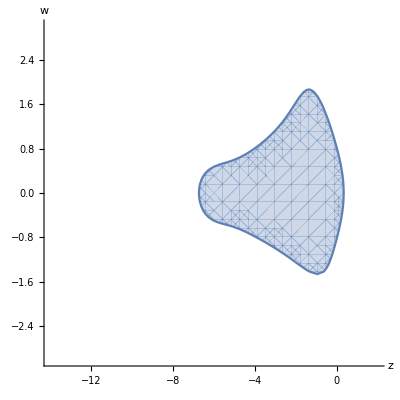

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.515667592014781,2.569283302176948,-1.569283302176948,0.2829359436434354,0.8267250785516251,-0.10966102219506012,0.7564661407610691,0.8618184526200139,0.13818154737998578,0.9404828519616463,0.24423674768607243,-0.18471959964771825,1.3256671229276307,1.8917788509943627,-0.6716517698645772,-0.40699403884182767,-0.2048806034850452,0.005675684983814938,-0.8697506206636301,-0.30002896369756066,-1.680831636489942,2.605724513606284,-1.0804364328776408,0.07798236572541666,0.055188849129415386,0.9184005556308551,-0.11032167485317859,0.1367322707198962,-0.2683865754389148,1.102050351437796,-0.19302503627866557,0.3593612603673628,0.04657484817622958,-0.19124588364505768,-0.16788364345845747,0.31255467890574495,1.2683865704233184,-1.102050345129326,0.19302503377795202,-0.3593612600292844,0.24669524697208975,-1.0129813047677578,0.5885959195911704,0.17769013873691494}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091820.comet-30-10

{0.0863604,0.243585,0.756415,0.702826,0.16459,0.132584,0.269697,-0.444596,1.4446,-0.367616,1.35396,0.0136551,-0.00579399,1.23479,-0.160793,2.89982,-0.903002,-0.504114,-0.519324,1.50816,-0.343398,0.90219,0.0446922,-0.105333,2.0795,-1.7288,-0.0496095,0.69891,-0.917618,1.25649,0.297493,0.363635,0.929716,-1.27306,0.154495,0.188844,1.91762,-1.25649,-0.297493,-0.363635,-0.926792,1.26905,2.9302,-3.27246}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

15.637

-Graphics3D-

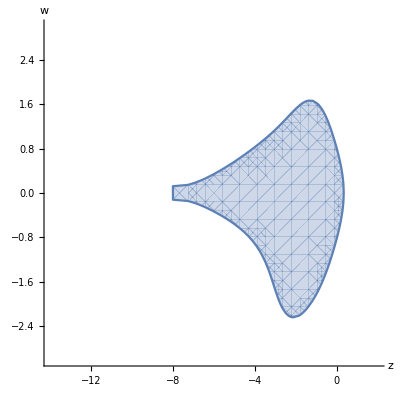

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.08636040433306086,0.24358463957600338,0.7564153564525098,0.7028261664628195,0.1645901921843511,0.13258364135282993,0.2696972016507347,-0.4445959998529416,1.4445959312810441,-0.3676155416922737,1.3539604551678892,0.01365508652438441,-0.005793992790204617,1.2347891713682322,-0.16079309269973258,2.899817598640882,-0.9030020850425404,-0.5041141076800456,-0.5193238082621228,1.5081602518941242,-0.3433984567713736,0.9021899615568271,0.04469223367803463,-0.10533279813889843,2.0795041234714877,-1.7288043702719986,-0.049609503166189964,0.6989097728790554,-0.9176183822725028,1.2564902709588972,0.2974927985409827,0.36363531324444565,0.9297160431603432,-1.2730555660727298,0.15449511398802032,0.18884443194349293,1.9176183364197235,-1.2564903109098984,-0.2974928693585341,-0.36363519884208917,-0.9267917974349112,1.2690511090868717,2.9301987896526844,-3.2724581094687735}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091822.comet-30-03

{0.175904,0.0928828,0.907117,-0.0143556,0.414378,0.599978,0.889603,0.927245,0.0727548,0.875049,0.146646,-0.0216954,0.631135,1.2084,0.359585,-0.0163923,2.08176,1.00494,-0.943188,-0.729354,-0.93061,2.64429,-0.395573,-0.449311,0.141797,0.434662,0.382562,0.0409793,-0.134073,1.21446,-0.372935,0.292545,-0.00940939,0.0852323,-0.351748,0.275925,1.13407,-1.21446,0.372935,-0.292545,0.134953,-1.22244,0.898952,0.18853}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

13.3821

-Graphics3D-

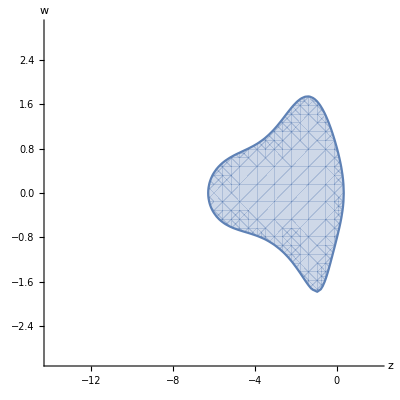

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.17590390926466773,0.09288283297439244,0.907117167025606,-0.014355575297533812,0.4143775307254068,0.5999780445720665,0.8896030864300392,0.9272451526247735,0.07275484668473085,0.8750493484914237,0.14664600715435241,-0.021695355645775932,0.6311345855958465,1.2083976159203267,0.35958491234432277,-0.01639228031206132,2.0817648526333294,1.0049443813708088,-0.9431877263586446,-0.7293536711325366,-0.9306103287455166,2.6442948838211087,-0.39557328419263027,-0.4493107982505883,0.14179707477200906,0.43466159968340295,0.3825620118933368,0.04097931353255643,-0.13407297255411588,1.214463060943416,-0.3729348568360816,0.2925447686141362,-0.009409386529169603,0.08523233133840824,-0.3517475800471512,0.2759246351574139,1.1340729737230884,-1.2144630627789301,0.37293485777228813,-0.2925447687362879,0.13495305946466846,-1.2224350798804147,0.8989522200400243,0.1885298004083994}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091839.comet-31-11

{0.156545,0.224704,0.775296,-0.19887,1.41324,-0.214371,0.461301,0.756025,0.243975,0.781895,0.329883,-0.111778,0.244443,1.38045,0.265667,-1.23301,0.386945,-0.800223,-0.679192,-0.17531,0.602085,1.88802,-0.769413,0.436217,0.836015,-0.398379,0.614504,-0.0521399,-0.424058,0.78719,0.403853,0.233015,0.50513,-0.937686,0.274294,0.158262,1.42406,-0.78719,-0.403853,-0.233015,-0.509819,0.94639,-1.17155,0.734982}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

11.9881

-Graphics3D-

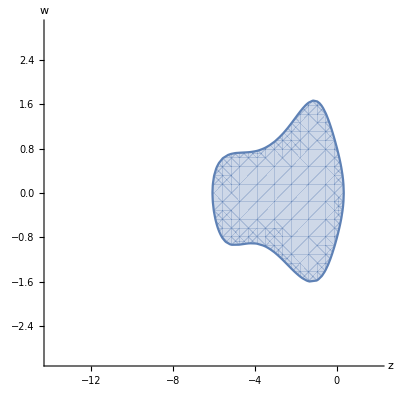

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.15654460552547503,0.22470428404276124,0.775295715957231,-0.19887031502205627,1.4132412502165186,-0.21437093520050568,0.46130136732096155,0.7560247662620583,0.24397523373794208,0.781894668005105,0.3298833473374693,-0.11177801534257448,0.24444294399625183,1.3804474651278897,0.26566671963039246,-1.2330075180539732,0.38694520100263163,-0.8002229628517528,-0.6791917012644134,-0.17531000866348964,0.6020853778823994,1.8880248266995063,-0.769413361866752,0.4362170565797002,0.8360150260175229,-0.3983791291655453,0.6145040218329516,-0.05213991847735284,-0.4240581071386014,0.7871898720855859,0.4038533706568127,0.2330148643999943,0.5051299175228209,-0.9376855380245659,0.27429385896308367,0.15826176188290003,1.4240581079513088,-0.7871898718352628,-0.40385337255709186,-0.2330148638111253,-0.5098192630469502,0.9463904894230717,-1.1715529171285441,0.7349816907364121}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091845.comet-30-03

{0.471202,0.19305,0.80695,-1.5157,1.05001,1.46568,0.532118,1.01117,-0.0111698,0.742261,0.324101,-0.0663622,0.950293,2.29045,-0.362521,0.0972631,2.9316,-0.479262,-0.729462,0.81005,0.107885,-0.569995,0.57707,1.9047,0.234613,0.50187,0.239336,0.0241813,-0.365137,0.780402,0.552008,0.0327263,0.375054,-0.801598,0.402672,0.0238719,1.36514,-0.780401,-0.552008,-0.0327264,-0.265082,0.566557,-0.995769,0.694294}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

13.7647

-Graphics3D-

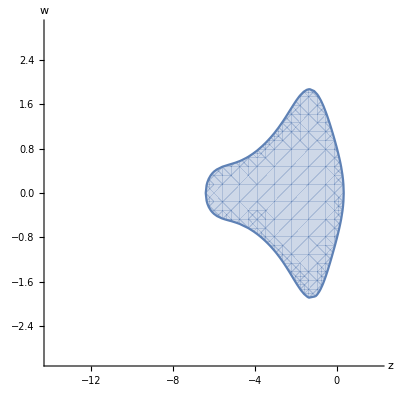

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.4712021787091427,0.19304972499278006,0.806950228438293,-1.515697513966146,1.0500135090349212,1.4656839840780584,0.5321175018003735,1.0111698309438153,-0.011169830943815474,0.7422609466945533,0.3241012419341768,-0.06636218862873046,0.9502925062378202,2.290451922616207,-0.36252099186799985,0.0972630564027931,2.931604215515843,-0.4792624831676963,-0.7294623970780314,0.8100499980971793,0.10788537341979575,-0.5699946770187582,0.5770696857863948,1.9047014078154147,0.23461251659334287,0.5018699579539367,0.23933636455438456,0.024181252559133545,-0.365136839207791,0.7804018711974765,0.5520084814453785,0.032726268976596896,0.37505374055313434,-0.8015977416649124,0.40267202857563794,0.02387193244448207,1.365136066022157,-0.7804014606805902,-0.5520081296232469,-0.032726432544562464,-0.2650821862054749,0.566557474575814,-0.9957688727378722,0.6942936135800686}]

higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091849.comet-31-05

{0.999981,1.05306,-0.0530648,1.71954,-1.84644,1.1269,0.771246,0.962541,0.037458,1.08906,-0.177915,0.0888559,1.33925,0.609253,0.23271,-0.521078,-0.386186,0.96193,0.878207,0.180389,-0.508171,1.12942,1.43703,-0.589034,0.499982,0.980545,-0.364449,-0.116077,0.0683598,-0.298837,0.941665,0.288812,-0.320512,1.40113,-0.826976,-0.253637,0.93164,0.298837,-0.941665,-0.288812,0.388587,-1.69871,0.476679,0.833447}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

14.8864

-Graphics3D-

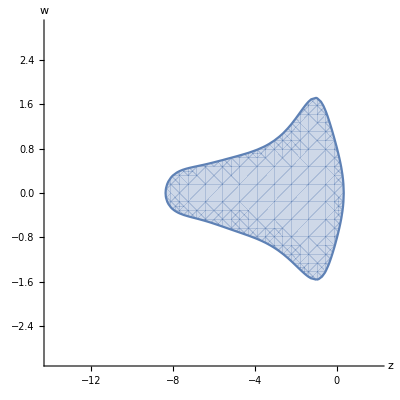

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.9999811737490213,1.0530647877575767,-0.05306480592419,1.7195364297157691,-1.846439386039415,1.126902952914844,0.7712459312402267,0.9625414439229061,0.03745795398800983,1.089058651890199,-0.177914905134314,0.08885593331660824,1.3392536798491173,0.6092526961926271,0.232709726275709,-0.5210780967049343,-0.38618581715835437,0.9619299654955125,0.8782067911654206,0.18038889438144076,-0.5081709511023393,1.1294220602229001,1.4370255160727319,-0.5890342831827863,0.49998158966488526,0.9805445778179069,-0.36444912323340806,-0.11607705273974993,0.06835980838950853,-0.2988371869560397,0.9416649208682668,0.2888124963191868,-0.3205124036446337,1.4011250521531897,-0.8269756348033076,-0.25363707357330395,0.9316402288892431,0.2988370601150284,-0.941664957762579,-0.28881243037335136,0.38858701342371577,-1.6987131918379648,0.4766794499501545,0.8334467066455673}]

higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

jOpt.9091850.comet-31-11

{0.437599,1.12629,-0.126293,2.7435,-2.30844,0.564938,0.983064,1.01369,-0.013685,0.946546,0.162825,-0.109371,0.905689,2.36772,-1.00334,4.54833,-3.25979,-0.626478,0.991496,0.898978,0.540177,-1.05527,-0.226139,0.20839,0.432131,0.120677,0.846664,-0.399472,-0.0102639,0.606033,-0.0665279,0.470759,-0.00690484,0.407698,0.0659621,-0.466756,1.01026,-0.606033,0.0665279,-0.470759,0.0377178,-2.22706,1.81409,0.375244}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

12.0493

-Graphics3D-

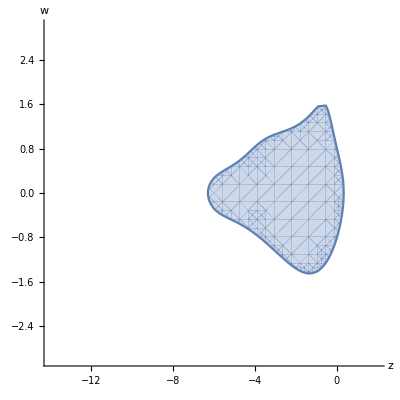

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.4375994243541199,1.1262932113510695,-0.1262932113511438,2.7435018363776025,-2.308439370174486,0.5649375336295896,0.9830638520032529,1.0136850031123066,-0.013685004183319296,0.9465457136035959,0.16282500750990206,-0.10937072111349715,0.9056885868805015,2.367721347709328,-1.0033351265380321,4.5483281464542475,-3.259794884871735,-0.6264781553638478,0.9914957659526419,0.8989778491417117,0.5401767076453329,-1.055273106462451,-0.22613929686772663,0.2083897119098106,0.4321312493819712,0.12067688911363866,0.8466642776420336,-0.39947241550703616,-0.010263862341279994,0.6060328052493497,-0.06652789517121757,0.47075895218032526,-0.0069048362304451405,0.40769822031050795,0.06596212325271135,-0.46675550663821574,1.0102638606005216,-0.6060328017997302,0.06652789256630501,-0.47075895116834593,0.03771776220257889,-2.2270567485717163,1.8140948267993176,0.37524416044180503}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```